# The Sinh-ArcSinh Family of Distributions

## Laurens Bogaardt | RIVM | SIM | 2019-09-13

Note that some functions in the Mathematica Notebook are marked as Initialisation Cells. This means that this Notebook can be imported by other Notebooks and these functions will be available there as well.

## The Sinh-ArcSinh Transformation

The Sinh-ArcSinh family of distributions [1], also referred to as the Jones distributions, is based on the Sinh-ArcSinh transformation. This transformation can adjust the skewnesses and the kurtosis in data.

```mathematica
jonesTransformation=Function[{x,c,d}, Sinh[d ArcSinh[x]-c]]
```

Function[{x,c,d},Sinh[d ArcSinh[x]-c]]

```mathematica
jonesInverseTransformation=Function[{x,c,d},Sinh[ArcSinh[x]/d+c/d]]
```

Function[{x,c,d},Sinh[ArcSinh[x]/d+c/d]]

```mathematica
Manipulate[Plot[{jonesTransformation[x,c,d],jonesInverseTransformation[x,c,d]},{x,-2,2},PlotRange->{{-2,2},{-2,2}}],{{c,0},-1,1,0.1},{{d,1},0.1,1,0.1}]
```

## The Sinh-ArcSinh Normal Distribution

When this transformation is applied to the normal distribution, a new distribution is obtained characterised by four parameters which control mean, variance, skewness and kurtosis.

### Transformation

Text

```mathematica
jonesNormalTransformation=Function[{x,a,b,c,d},jonesTransformation[(x-a)/b,c,d]]
```

Function[{x,a,b,c,d},jonesTransformation[(x-a)/b,c,d]]

```mathematica
jonesNormalInverseTransformation=Function[{x,a,b,c,d},a+b jonesInverseTransformation[x,c,d]]
```

Function[{x,a,b,c,d},a+b jonesInverseTransformation[x,c,d]]

```mathematica
Manipulate[Plot[{jonesNormalTransformation[x,a,b,c,d],jonesNormalInverseTransformation[x,a,b,c,d]},{x,-2,2},PlotRange->{{-2,2},{-2,2}}],{{a,0},-1,1,0.1},{{b,1},0.1,1,0.1},{{c,0},-1,1,0.1},{{d,1},0.1,1,0.1}]
```

### Distribution

Text

### PDF

Text

```mathematica
jonesDistribution=Function[{x,a,b,c,d},Evaluate[Simplify[d Sqrt[(1+jonesNormalTransformation[x,a,b,c,d]^2)/(b^2+(x-a)^2)]PDF[NormalDistribution[],jonesNormalTransformation[x,a,b,c,d]]]]]
```

Function[{x,a,b,c,d},(d ⅇ^(-1/2 Sinh[c+d ArcSinh[(a-x)/b]]^2) √(Cosh[c+d ArcSinh[(a-x)/b]]^2/(a^2+b^2-2 a x+x^2)))/(√(2 π))]

```mathematica
Manipulate[Plot[{jonesDistribution[x,a,b,c,d]},{x,-3,3},PlotRange->{{-3,3},{0,1}},ImageSize->400],{{a,0},-1,1,0.1},{{b,1},0.1,2,0.1},{{c,0},-1,1,0.1},{{d,1},0.1,2,0.1}]
```

### CDF

Text

```mathematica
jonesCumulativeDistribution=Function[{x,a,b,c,d},Evaluate[1/2+Integrate[jonesDistribution[x,a,b,c,d],x]]]
```

Function[{x,a,b,c,d},1/2-1/2 b √(1+(a-x)^2/b^2) √(Cosh[c+d ArcSinh[(a-x)/b]]^2/(a^2+b^2-2 a x+x^2)) Erf[Sinh[c+d ArcSinh[(a-x)/b]]/(√2)] Sech[c+d ArcSinh[(a-x)/b]]]

```mathematica
Manipulate[Plot[{jonesCumulativeDistribution[x,a,b,c,d]},{x,-3,3},PlotRange->{{-3,3},{0,1}},ImageSize->400],{{a,0},-1,1,0.1},{{b,1},0.1,2,0.1},{{c,0},-1,1,0.1},{{d,1},0.1,2,0.1}]
```

### Inverse CDF

Text

```mathematica
jonesInverseCumulativeDistribution=Function[{x,a,b,c,d},Evaluate[First[y/.Quiet[Solve[jonesCumulativeDistribution[y,a,b,c,d]==x,y]]]]]
```

Function[{x,a,b,c,d},a-b Sinh[(-c+ArcSinh[√2 InverseErf[1-2 x]])/d]]

```mathematica
Manipulate[Plot[{jonesInverseCumulativeDistribution[x,a,b,c,d]},{x,0,1},PlotRange->{{0,1},{-3,3}},ImageSize->400],{{a,0},-1,1,0.1},{{b,1},0.1,2,0.1},{{c,0},-1,1,0.1},{{d,1},0.1,2,0.1}]
```

### Moments

Text

```mathematica
jonesBessels=Function[{q},Exp[1/4]/Sqrt[8Pi](BesselK[(q+1)/2,1/4]+BesselK[(q-1)/2,1/4])]
```

Function[{q},(Exp[1/4] (BesselK[(q+1)/2,1/4]+BesselK[(q-1)/2,1/4]))/(√(8 π))]

```mathematica
jonesMomentsWithoutLocation=Function[{m,b,c,d},(b/2)^m Sum[Binomial[m,i](-1)^i Exp[(m-2i)c/d]jonesBessels[(m-2i)/d],{i,0,m}]]
```

Function[{m,b,c,d},(b/2)^m ∑_(i=0)^m Binomial[m,i] (-1)^i Exp[((m-2 i) c)/d] jonesBessels[(m-2 i)/d]]

```mathematica
jonesMomentsAboutLocation=Function[{m,l,b,c,d},jonesMomentsWithoutLocation[m,b,c,d]+Sum[Binomial[m,i]jonesMomentsWithoutLocation[i,b,c,d](-l)^(m-i),{i,0,m-1}]]
```

Function[{m,l,b,c,d},jonesMomentsWithoutLocation[m,b,c,d]+∑_(i=0)^(m-1) Binomial[m,i] jonesMomentsWithoutLocation[i,b,c,d] (-l)^(m-i)]

```mathematica
jonesRawMoments=Function[{m,a,b,c,d},jonesMomentsAboutLocation[m,-a,b,c,d]]
```

Function[{m,a,b,c,d},jonesMomentsAboutLocation[m,-a,b,c,d]]

```mathematica
jonesCentralMoments=Function[{m,a,b,c,d},With[{mean=a+jonesMomentsAboutLocation[1,a,b,c,d]},jonesMomentsAboutLocation[m,mean,b,c,d]]]
```

Function[{m,a,b,c,d},With[{mean=a+jonesMomentsAboutLocation[1,a,b,c,d]},jonesMomentsAboutLocation[m,mean,b,c,d]]]

```mathematica
jonesStandardisedMoments=Function[{m,a,b,c,d},With[{mean=a+jonesMomentsAboutLocation[1,a,b,c,d]},With[{variance=jonesMomentsAboutLocation[2,mean,b,c,d]},jonesMomentsAboutLocation[m,mean,b,c,d]/variance^(m/2)]]]
```

Function[{m,a,b,c,d},With[{mean=a+jonesMomentsAboutLocation[1,a,b,c,d]},With[{variance=jonesMomentsAboutLocation[2,mean,b,c,d]},jonesMomentsAboutLocation[m,mean,b,c,d]/variance^(m/2)]]]

### Find Distribution Parameters

Text

```mathematica
jonesFindDistributionParameters[mean_,variance_,skewness_,kurtosis_]:={a,Exp[logb],c,Exp[logd]}/.FindRoot[{mean,variance,skewness,kurtosis}=={jonesRawMoments[1,a,Exp[logb],c,Exp[logd]],jonesCentralMoments[2,a,Exp[logb],c,Exp[logd]],jonesStandardisedMoments[3,a,Exp[logb],c,Exp[logd]],jonesStandardisedMoments[4,a,Exp[logb],c,Exp[logd]]},{{a,mean},{logb,Log[variance]},{c,0.0},{logd,0.0}}]
```

```mathematica
jonesFindDistributionParameters[data_List]:=With[{mean=Mean[data],variance=Variance[data],skewness=Skewness[data],kurtosis=Kurtosis[data]},jonesFindDistributionParameters[mean,variance,skewness,kurtosis]]
```

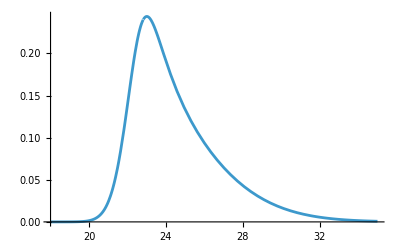
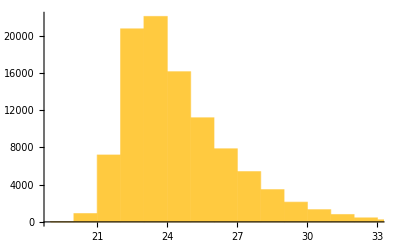
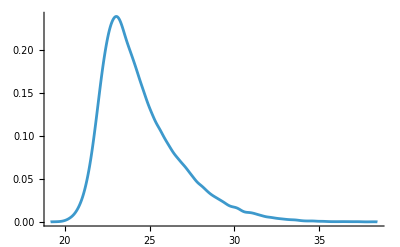
Input | 24.5 | 5.3 | 1.2 | 4.8
Generated | 24.4968 | 5.30957 | 1.19904 | 4.7856
Parameters | 22.8233 | 1.38156 | 0.648131 | 0.869453
Plots | -Graphics- | -Graphics- | -Graphics- |

```mathematica
With[{mean=24.5,variance=5.3,skewness=1.2,kurtosis=4.8,n=100000},With[{parameters=jonesFindDistributionParameters[mean,variance,skewness,kurtosis]},With[{data=jonesInverseCumulativeDistribution[RandomReal[{0,1},n],parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]]]},Grid[{{"Input",mean,variance,skewness,kurtosis},{"Generated",Mean[data],Variance[data],Skewness[data],Kurtosis[data]},Join[{"Parameters"},parameters],{"Plots",Plot[{jonesDistribution[x,parameters[[1]],parameters[[2]],parameters[[3]],parameters[[4]]]},{x,18,35}],Histogram[data],SmoothHistogram[data]}}]]]]
```

## References

[1] Jones and Pewsey, Sinh-arcsinh distributions, Biometrika, Volume 96, Issue 4, December 2009, Pages 761–780, https://doi.org/10.1093/biomet/asp053